```mathematica
(* Simulate the BK compounding process *)
```

```mathematica
?OrnsteinUhlenbeckProcess
```

```mathematica
data4OU=RandomFunction[OrnsteinUhlenbeckProcess[0,.5,.1],{0,1,0.01},5]
```

TemporalData[…]

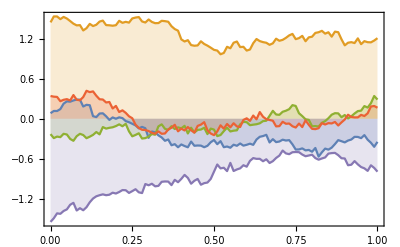

```mathematica
ListLinePlot[data4OU,Filling->Axis, Frame -> True]
```

```mathematica
Export["/Users/danpirjol/statmech/jmp/book/figures/5OUpaths.eps",%1493,"EPS"]
```

/Users/danpirjol/statmech/jmp/book/figures/5OUpaths.eps

```mathematica
sample[θ_]:=(SeedRandom[14];RandomFunction[OrnsteinUhlenbeckProcess[0,1,θ],{0,1,.01}])
```

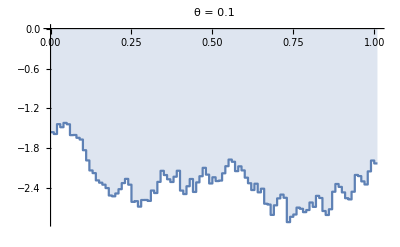
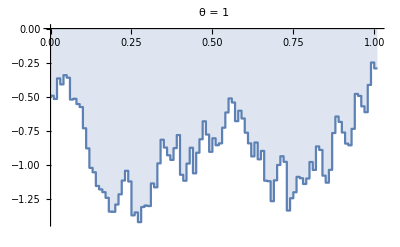
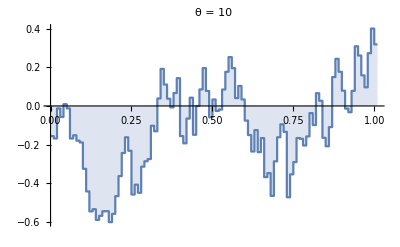

```mathematica
ListStepPlot[sample[#],Filling->Axis,PlotLabel->StringJoin["θ = ", ToString[#]]]&/@{.1,1,10}
```

```mathematica
(* Generate paths of the OU process *)
```

```mathematica
NCDF[x_] :=1/2(1+Erf[x/Sqrt[2]])
```

```mathematica
InvN[u_] := Sqrt[2] InverseErf[2u-1]
```

```mathematica
OUpath[sig_,gamma_,n_]:=Module[{z1,z2,tau},Clear[zlist];tau=0.01;zf=Exp[-gamma tau];DeltaG=sig^2/(2gamma)(1-zf^2);varZ=sig^2/(2gamma);z1=Sqrt[varZ] InvN[Random[]];zlist={{1,z1}};Do[{z2=z1 zf+Sqrt[DeltaG] InvN[Random[]];z1=z2;zlist= Append[zlist, {i,z2}]}, {i,2,n}]]
```

```mathematica
OUpath[0.1,0.5,100]
```

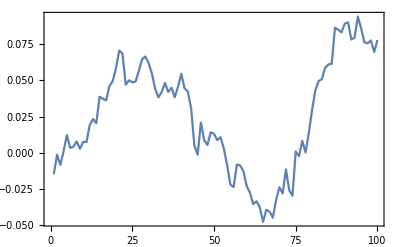

```mathematica
ListPlot[zlist,Joined -> True, Frame -> True]
```

```mathematica
(* Test the E[Z(t)]=0 and martingale property of Exp[Z(n)-1/2 var(Z(n))] *)
```

```mathematica
SimulationTest[sig_,gamma_,n_,nmc_] := Module[{tsum,zval,expval,varZ,sum1,sum2,meanB,varB},Clear[zlist,sum1,sum2];tau=0.01;sum1=0;sum2=0;Do[{OUpath[sig,gamma,n];
zval =zlist[[n]][[2]]; varZ = sig^2/(2gamma);expval=Exp[zval-0.5 varZ];tsum=zval;sum1=sum1+tsum;sum2=sum2+tsum^2}, {j,1,nmc}];meanB=sum1/nmc;varB = 1/nmc sum2-(sum1/nmc)^2;Print["sig= ",sig," mean = ",meanB," var = ",varB];{sig,meanB,Sqrt[varB/nmc]}]
```

```mathematica
SimulationTest[0.3,0.5,100,1000]
```

sig= 0.3 mean = -0.0125039 var = 0.0810986

{0.3,-0.0125039,0.00900547}

```mathematica
0.2^2/(2 0.5)
```

0.04

```mathematica
SimulationTest[0.1,0.1,100,10000]
```

sig= 0.1 mean = 0.995971 var = 0.0514599

{0.1,0.995971,0.00226848}

```mathematica
(* Compounding process B(i+1)=(1+mu(i))*B(i) with stationary OU process Z(t) *)
```

```mathematica
BKpathgen[sig_,gamma_,n_] := Module[{v1,v2,mu},Clear[Blist,zlist];
rho=0.025;
Blist={{1,1}};varZ=sig^2/(2gamma);OUpath[sig,gamma,n];
v1=1;Do[{mu=rho Exp[zlist[[i]][[2]]-1/2 varZ ];v2=(1+mu) v1;v1=v2;(* Print[i," , ",v2," , ",mu];*)Blist= Append[Blist, {i,v2}]}, {i,2,n}]]
```

```mathematica
zlist[[1]][[2]]
```

0.0308963

```mathematica
BKpathgen[0.1,0.5,100]
```

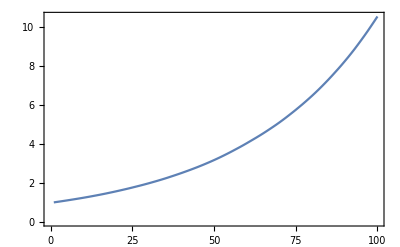

```mathematica
ListPlot[Blist,Joined -> True, Frame -> True]
```

```mathematica
(* Main simulation function *)
```

```mathematica
BKsimulation[sig_,gamma_,n_,nmc_] := Module[{tsum,sum1,sum2,meanB,varB},Clear[Blist,sum1,sum2];sum1=0;sum2=0;Do[{BKpathgen[sig,gamma,n];
tsum =Blist[[n]][[2]]; sum1=sum1+tsum;(* Print[tsum]; *)sum2=sum2+tsum^2}, {j,1,nmc}];
meanB=sum1/nmc;varB = 1/nmc sum2-(sum1/nmc)^2;Print["sig= ", sig," mean = ",meanB," err = ",Sqrt[varB/nmc]];{sig,meanB,varB}]
```

```mathematica
BKsimulation[0.001,0.1,10,20]
```

sig= 0.001 mean = 1.24885 err = 0.000116043

{0.001,1.24885,2.6932×10^-7}

```mathematica
BKdeterministic[rho_,n_] := (1+rho)^(n-1)
```

```mathematica
BKdeterministic[0.025,10]
```

1.24886

```mathematica
(* Fix gamma = 0.1 and compute E[B(n)] for several sigma; n=100,tau=0.01 *)
```

```mathematica
BKsimulation[0.01,0.1,100,1000]
```

sig= 0.01 mean = 11.5439 err = 0.0190331

{0.01,11.5439,0.36226}

```mathematica
Clear[BKres1table]
```

```mathematica
BKres1table={};
```

```mathematica
Do[BKres1table= Append[BKres1table, BKsimulation[0.01 i1,0.1,100,1000]], {i1,5,50,5}]
```

sig= 0.05 mean = 12.03 err = 0.109478

sig= 0.1 mean = 13.9427 err = 0.3245

sig= 0.15 mean = 17.3062 err = 0.826799

sig= 0.2 mean = 36.4591 err = 6.93042

sig= 0.25 mean = 380.806 err = 154.494

sig= 0.3 mean = 930.871 err = 517.597

sig= 0.35 mean = 10737.7 err = 6686.41

sig= 0.4 mean = 5.56827×10^13 err = 5.56405×10^13

sig= 0.45 mean = 1.18461×10^11 err = 1.12783×10^11

sig= 0.5 mean = 2.23891×10^11 err = 2.05373×10^11

```mathematica
TableForm[BKres1table]
```

0.05 | 12.03 | 11.9855
0.1 | 13.9427 | 105.3
0.15 | 17.3062 | 683.596
0.2 | 36.4591 | 48030.7
0.25 | 380.806 | 2.38684×10^7
0.3 | 930.871 | 2.67907×10^8
0.35 | 10737.7 | 4.4708×10^10
0.4 | 5.56827×10^13 | 3.09586×10^30
0.45 | 1.18461×10^11 | 1.272×10^25
0.5 | 2.23891×10^11 | 4.21781×10^25

```mathematica
BKgamma0p25table={};
```

```mathematica
BKsimulation[0.01,0.25,100,1000]
```

sig= 0.01 mean = 11.5186 err = 0.0122233

{0.01,11.5186,0.14941}

```mathematica
Do[BKgamma0p25table= Append[BKgamma0p25table, BKsimulation[0.01 i1,0.25,100,1000]], {i1,5,50,5}]
```

sig= 0.05 mean = 11.7535 err = 0.0621906

sig= 0.1 mean = 12.0193 err = 0.138134

sig= 0.15 mean = 13.1161 err = 0.256146

sig= 0.2 mean = 15.6668 err = 0.76071

sig= 0.25 mean = 17.6356 err = 0.93266

sig= 0.3 mean = 24.6082 err = 2.77767

sig= 0.35 mean = 76.0863 err = 24.0276

sig= 0.4 mean = 55961.6 err = 55629.8

sig= 0.45 mean = 3154.09 err = 2997.04

sig= 0.5 mean = 8567.24 err = 7859.34

```mathematica
TableForm[BKgamma0p25table]
```

0.05 | 11.7535 | 3.86767
0.1 | 12.0193 | 19.081
0.15 | 13.1161 | 65.6109
0.2 | 15.6668 | 578.68
0.25 | 17.6356 | 869.854
0.3 | 24.6082 | 7715.45
0.35 | 76.0863 | 577328.
0.4 | 55961.6 | 3.09468×10^12
0.45 | 3154.09 | 8.98223×10^9
0.5 | 8567.24 | 6.17692×10^10

```mathematica
Clear[BKgamma0p5table]
```

```mathematica
BKgamma0p5table={};
```

```mathematica
Do[BKgamma0p5table= Append[BKgamma0p5table, BKsimulation[0.01 i1,0.5,100,1000]], {i1,5,50,5}]
```

sig= 0.05 mean = 11.5861 err = 0.0400224

sig= 0.1 mean = 11.978 err = 0.0917955

sig= 0.15 mean = 12.3895 err = 0.143838

sig= 0.2 mean = 12.8035 err = 0.219588

sig= 0.25 mean = 13.6792 err = 0.389599

sig= 0.3 mean = 18.3186 err = 2.38842

sig= 0.35 mean = 19.5375 err = 1.41725

sig= 0.4 mean = 22.2727 err = 2.1351

sig= 0.45 mean = 26.4949 err = 2.36771

sig= 0.5 mean = 41.6748 err = 8.28339

```mathematica
TableForm[BKgamma0p5table]
```

0.05 | 11.5861 | 1.6018
0.1 | 11.978 | 8.42641
0.15 | 12.3895 | 20.6894
0.2 | 12.8035 | 48.2191
0.25 | 13.6792 | 151.787
0.3 | 18.3186 | 5704.54
0.35 | 19.5375 | 2008.6
0.4 | 22.2727 | 4558.63
0.45 | 26.4949 | 5606.06
0.5 | 41.6748 | 68614.6

```mathematica
BKsimulation[0.01,0.5,100,1000]
```

sig= 0.01 mean = 11.5278 err = 0.00831461

{0.01,11.5278,0.0691327}

```mathematica
BKgamma1p0table={};
```

```mathematica
Do[BKgamma1p0table= Append[BKgamma1p0table, BKsimulation[0.01 i1,1.0,100,1000]], {i1,5,50,5}]
```

sig= 0.05 mean = 11.5137 err = 0.0279858

sig= 0.1 mean = 11.6007 err = 0.0552608

sig= 0.15 mean = 11.8983 err = 0.0898226

sig= 0.2 mean = 11.9835 err = 0.11882

sig= 0.25 mean = 12.4933 err = 0.187996

sig= 0.3 mean = 12.456 err = 0.184648

sig= 0.35 mean = 13.4677 err = 0.289167

sig= 0.4 mean = 14.238 err = 0.374906

sig= 0.45 mean = 15.7261 err = 0.671869

sig= 0.5 mean = 15.558 err = 0.625994

```mathematica
TableForm[BKgamma1p0table]
```

0.05 | 11.5137 | 0.783208
0.1 | 11.6007 | 3.05375
0.15 | 11.8983 | 8.06811
0.2 | 11.9835 | 14.1183
0.25 | 12.4933 | 35.3426
0.3 | 12.456 | 34.0949
0.35 | 13.4677 | 83.6177
0.4 | 14.238 | 140.555
0.45 | 15.7261 | 451.408
0.5 | 15.558 | 391.869

```mathematica
Clear[BKres2table]
```

```mathematica
BKres2table={};
```

```mathematica
Do[BKres2table= Append[BKres2table, BKsimulation[0.01 i1,0.1,100,10000]], {i1,1,40}]
```

sig= 0.01 mean = 11.5347 err = 0.00615317

sig= 0.02 mean = 11.5956 err = 0.0122746

sig= 0.03 mean = 11.652 err = 0.0186588

sig= 0.04 mean = 11.7901 err = 0.0256056

sig= 0.05 mean = 11.9777 err = 0.033991

sig= 0.06 mean = 12.1357 err = 0.041866

sig= 0.07 mean = 12.3623 err = 0.053743

sig= 0.08 mean = 12.7994 err = 0.0657889

$Aborted

```mathematica
TableForm[BKres2table]
```

0.01 | 11.5347 | 0.378615
0.02 | 11.5956 | 1.50666
0.03 | 11.652 | 3.4815
0.04 | 11.7901 | 6.55647
0.05 | 11.9777 | 11.5539
0.06 | 12.1357 | 17.5276
0.07 | 12.3623 | 28.8831
0.08 | 12.7994 | 43.2818

```mathematica
BKsimulation[0.1,0.1,100,1000]
```

mean = 11.0445 var = 3.76066

```mathematica
BKdeterministic[0.025,100]
```

11.5256

```mathematica
BKres3table={};
```

```mathematica
Do[BKres3table= Append[BKres3table, {BKsimulation[0.01 i1,0.1,100,1000],BKsimulation[0.01 i1,0.2,100,1000]}], {i1,1,5}]
```

sig= 0.01 mean = 11.5476 err = 0.0197484

sig= 0.01 mean = 11.5142 err = 0.0137995

sig= 0.02 mean = 11.6479 err = 0.0392498

sig= 0.02 mean = 11.5509 err = 0.0263602

sig= 0.03 mean = 11.713 err = 0.0601518

sig= 0.03 mean = 11.6113 err = 0.0417705

sig= 0.04 mean = 11.8798 err = 0.0842319

sig= 0.04 mean = 11.555 err = 0.0522673

sig= 0.05 mean = 12.0352 err = 0.108726

sig= 0.05 mean = 11.8186 err = 0.0694954

```mathematica
TableForm[BKres3table]
```

0.01
11.5476
0.389999 | 0.01
11.5142
0.190426
0.02
11.6479
1.54055 | 0.02
11.5509
0.694858
0.03
11.713
3.61824 | 0.03
11.6113
1.74477
0.04
11.8798
7.09502 | 0.04
11.555
2.73187
0.05
12.0352
11.8214 | 0.05
11.8186
4.82961

```mathematica
BKExpectationBnSimulation[sig_,gamma_,n_,nmc_] := Module[{tsum,sum1,sum2,meanB,varB,errmean,errLam},Clear[Blist,zlist,sum1,sum2];sum1=0;sum2=0;Do[{BKpathgen[sig,gamma,n];
tsum =Blist[[n]][[2]]; sum1=sum1+tsum;(* Print[tsum]; *) sum2=sum2+tsum^2}, {j,1,nmc}];
meanB=sum1/nmc;varB = 1/nmc sum2-(sum1/nmc)^2;
errmean=Sqrt[varB/nmc];errLam=0.01Log[1+errmean/meanB ];Print["sig= ", sig," mean = ",meanB," err = ",Sqrt[varB/nmc]];{sig,Around[meanB,errmean]} ]
```

```mathematica
BKLyapunovSimulation[sig_,gamma_,n_,nmc_] := Module[{tsum,sum1,sum2,meanB,varB,errmean,errLam},Clear[Blist,zlist,sum1,sum2];sum1=0;sum2=0;Do[{BKpathgen[sig,gamma,n];
tsum =Blist[[n]][[2]]; sum1=sum1+tsum;(* Print[tsum]; *) sum2=sum2+tsum^2}, {j,1,nmc}];
meanB=sum1/nmc;varB = 1/nmc sum2-(sum1/nmc)^2;
errmean=Sqrt[varB/nmc];errLam=0.01Log[1+errmean/meanB ];Print["sig= ", sig," mean = ",meanB," err = ",Sqrt[varB/nmc]];(* {sig,Around[meanB,errmean]} *) {sig,Around[0.01 Log[meanB],errLam]} ]
```

```mathematica
BKLyapunovSimulation[0.3,0.1,100,10]
```

2.3215

16.6962

116.583

267.712

7.36089

63.0014

2.36128

425.942

47.0127

1.44315

sig= 0.3 mean = 95.0435 err = 42.7646

{0.3,95.43.}

```mathematica
BKLyapunovSimulation[0.3,0.5,100,10]
```

22.1132

15.2879

13.4344

15.039

12.9736

15.4659

26.0669

11.1021

4.41336

15.0029

sig= 0.3 mean = 15.0899 err = 1.75249

{0.3,15.11.8}

```mathematica
Clear[res1table]
```

```mathematica
res1table={};
```

```mathematica
Do[res1table= Append[res1table, BKLyapunovSimulation[0.01 i1,0.1,100,1000]], {i1,1,40}]
```

sig= 0.01 mean = 11.5459 err = 0.0199311

sig= 0.02 mean = 11.6627 err = 0.0404282

sig= 0.03 mean = 11.7784 err = 0.0599648

sig= 0.04 mean = 11.8213 err = 0.0801934

sig= 0.05 mean = 12.0772 err = 0.113153

sig= 0.06 mean = 12.0916 err = 0.131411

sig= 0.07 mean = 12.5685 err = 0.168854

sig= 0.08 mean = 12.6516 err = 0.198741

sig= 0.09 mean = 12.9787 err = 0.28478

sig= 0.1 mean = 14.1095 err = 0.373612

sig= 0.11 mean = 14.4552 err = 0.392116

sig= 0.12 mean = 14.3867 err = 0.427853

sig= 0.13 mean = 15.7547 err = 0.691154

sig= 0.14 mean = 18.1511 err = 1.18594

sig= 0.15 mean = 18.8632 err = 0.996554

sig= 0.16 mean = 23.7449 err = 2.55334

sig= 0.17 mean = 22.0294 err = 2.39803

sig= 0.18 mean = 52.1033 err = 29.4795

sig= 0.19 mean = 32.4835 err = 6.88397

sig= 0.2 mean = 65.4838 err = 24.1896

sig= 0.21 mean = 83.7522 err = 33.269

sig= 0.22 mean = 40.4674 err = 11.8946

sig= 0.23 mean = 615.304 err = 569.094

sig= 0.24 mean = 123.567 err = 33.0822

sig= 0.25 mean = 6188.69 err = 6121.75

sig= 0.26 mean = 409.592 err = 236.018

sig= 0.27 mean = 1246.06 err = 706.272

sig= 0.28 mean = 265.101 err = 120.71

sig= 0.29 mean = 11179.2 err = 9636.24

sig= 0.3 mean = 553961. err = 552139.

sig= 0.31 mean = 1906.84 err = 1041.57

sig= 0.32 mean = 3556.37 err = 1981.07

sig= 0.33 mean = 2.79242×10^6 err = 1.9781×10^6

sig= 0.34 mean = 3666.14 err = 2017.94

sig= 0.35 mean = 3.84226×10^7 err = 3.53468×10^7

sig= 0.36 mean = 1.07018×10^6 err = 1.02545×10^6

sig= 0.37 mean = 63695.5 err = 38840.9

sig= 0.38 mean = 328861. err = 320170.

sig= 0.39 mean = 4.16418×10^7 err = 3.51164×10^7

sig= 0.4 mean = 4.44574×10^10 err = 4.44273×10^10

```mathematica
0.01 Log[11.524]
```

0.0244443

```mathematica
res1tableErr={{0.01,0.024},{0.02,0.024},{0.03,0.025}};
```

```mathematica
res1table
```

{{0.01,11.5460.020},{0.02,11.660.04},{0.03,11.780.06},{0.04,11.820.08},{0.05,12.080.11},{0.06,12.090.13},{0.07,12.570.17},{0.08,12.650.20},{0.09,12.980.28},{0.1,14.10.4},{0.11,14.50.4},{0.12,14.40.4},{0.13,15.80.7},{0.14,18.21.2},{0.15,18.91.0},{0.16,23.72.6},{0.17,22.02.4},{0.18,52.29.},{0.19,32.7.},{0.2,65.24.},{0.21,84.33.},{0.22,40.12.},{0.23,615.569.},{0.24,124.33.},{0.25,6.6.10^3},{0.26,410.236.},{0.27,1246.706.},{0.28,265.121.},{0.29,1.11.010^4},{0.3,6.6.10^5},{0.31,1.91.010^3},{0.32,3.62.010^3},{0.33,2.82.010^6},{0.34,3.72.010^3},{0.35,3.83.510^7},{0.36,1.11.010^6},{0.37,6.4.10^4},{0.38,3.33.210^5},{0.39,4.23.510^7},{0.4,4.4.10^10}}

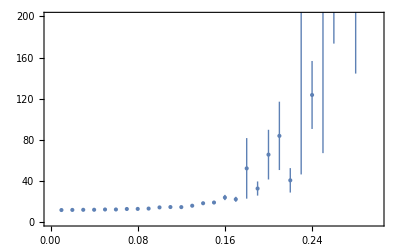

```mathematica
ListPlot[res1table, Frame -> True, PlotRange -> {{0,0.3},{0,200}}]
```

```mathematica
BKdeterministic[0.025,100]
```

11.5256

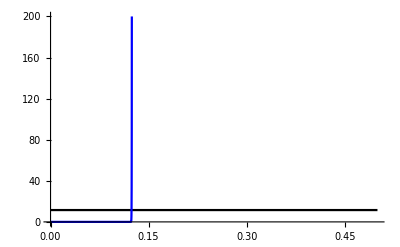

```mathematica
Plot[{11.5256,Exp[100lowBound[x,0.025,4.84,100,0.01]]},{x,0,0.5}, PlotStyle -> {Black,Blue}, PlotRange -> {0,200}]
```

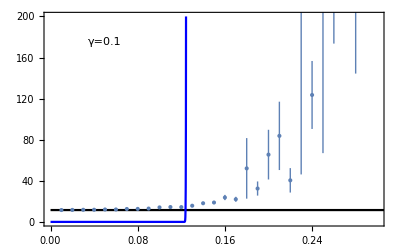

```mathematica
Show[%1022,%1018,Epilog-> {Text[Style["γ=0.1",Medium], {0.05,175}]}]
```

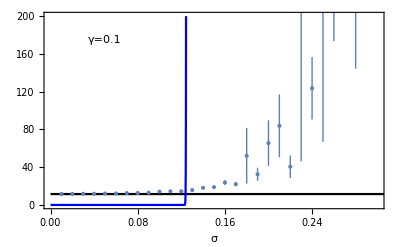

```mathematica
Show[%1023,FrameLabel->{{None,None},{HoldForm[σ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/danpirjol/statmech/jmp/BKcompounding/MCgamma0p1.eps",%1026,"EPS"]
```

/Users/danpirjol/statmech/jmp/BKcompounding/MCgamma0p1.eps

```mathematica
(* Plot of the Lyapunov exponent *)
```

```mathematica
resLyapTable={};
```

```mathematica
Do[resLyapTable= Append[resLyapTable, BKLyapunovSimulation[0.01 i1,0.1,100,1000]], {i1,1,30}]
```

sig= 0.01 mean = 11.5486 err = 0.0190208

sig= 0.02 mean = 11.6773 err = 0.0392574

sig= 0.03 mean = 11.6142 err = 0.0582242

sig= 0.04 mean = 11.8472 err = 0.0817107

sig= 0.05 mean = 11.963 err = 0.103202

sig= 0.06 mean = 12.255 err = 0.142748

sig= 0.07 mean = 12.6951 err = 0.180826

sig= 0.08 mean = 12.6088 err = 0.190936

sig= 0.09 mean = 13.0193 err = 0.234583

sig= 0.1 mean = 12.9636 err = 0.256259

sig= 0.11 mean = 13.6768 err = 0.343201

sig= 0.12 mean = 14.5368 err = 0.443952

sig= 0.13 mean = 14.8878 err = 0.441299

sig= 0.14 mean = 16.4242 err = 1.23046

sig= 0.15 mean = 19.8381 err = 1.33543

sig= 0.16 mean = 19.5173 err = 1.13645

sig= 0.17 mean = 28.1819 err = 5.36992

sig= 0.18 mean = 24.0854 err = 2.93374

sig= 0.19 mean = 50.0251 err = 14.5372

sig= 0.2 mean = 22.9579 err = 2.05408

sig= 0.21 mean = 46.8131 err = 10.691

sig= 0.22 mean = 57.5545 err = 17.9181

sig= 0.23 mean = 99.9372 err = 34.5423

sig= 0.24 mean = 134.024 err = 59.1205

sig= 0.25 mean = 70.5884 err = 23.811

sig= 0.26 mean = 182.32 err = 62.6787

sig= 0.27 mean = 1550.02 err = 1300.8

sig= 0.28 mean = 150.802 err = 46.0266

sig= 0.29 mean = 285.037 err = 126.259

sig= 0.3 mean = 1778.25 err = 918.919

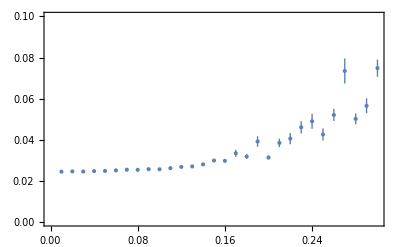

```mathematica
ListPlot[resLyapTable, Frame -> True, PlotRange -> {{0,0.3},{0,0.1}}]
```

```mathematica
lowBound[sig_,rho_,k_,n_,tau_] :=  Log[rho]+k 1/2 sig^2 n^2 tau
```

```mathematica
kf[0.1]
```

4.83742

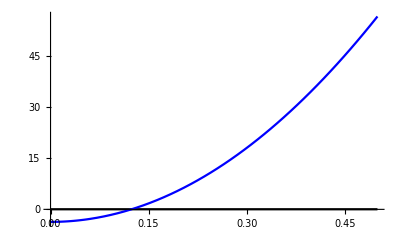

```mathematica
Plot[{Log[1.025],lowBound[x,0.025,kf[0.1],100,0.01]},{x,0,0.5}, PlotStyle -> {Black,Blue}]
```

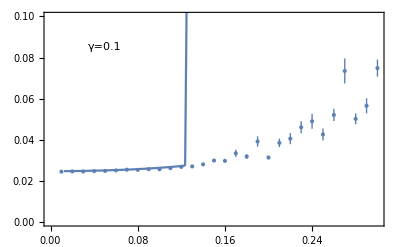

```mathematica
Show[%1034,%1322,Epilog-> {Text[Style["γ=0.1",Medium], {0.05,0.085}]}]
```

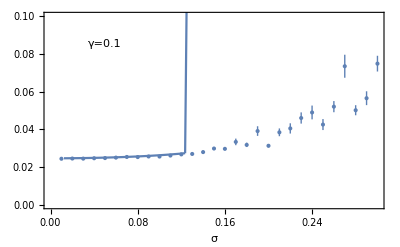

```mathematica
Show[%1325,FrameLabel->{{None,None},{HoldForm[σ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/danpirjol/statmech/jmp/BKcompounding/LyapMCgamma0p1.eps",%1326,"EPS"]
```

/Users/danpirjol/statmech/jmp/BKcompounding/LyapMCgamma0p1.eps

```mathematica
(* Same with gamma=0.5 *)
```

```mathematica
Clear[res5table]
```

```mathematica
res5table={};
```

```mathematica
Do[res5table= Append[res5table, BKLyapunovSimulation[0.01 i1,0.5,100,1000]], {i1,41,50}]
```

sig= 0.41 mean = 21.127 err = 2.21143

sig= 0.42 mean = 33.5694 err = 12.1687

sig= 0.43 mean = 25.3003 err = 3.09692

sig= 0.44 mean = 44.6339 err = 12.4387

sig= 0.45 mean = 25.4347 err = 2.86231

sig= 0.46 mean = 32.2602 err = 4.50084

sig= 0.47 mean = 51.5023 err = 23.5699

sig= 0.48 mean = 34.356 err = 5.32702

sig= 0.49 mean = 115.052 err = 87.1395

sig= 0.5 mean = 174.282 err = 116.963

```mathematica
res5table
```

{{0.01,11.5460.020},{0.02,11.660.04},{0.03,11.780.06},{0.04,11.820.08},{0.05,12.080.11},{0.06,12.090.13},{0.07,12.570.17},{0.08,12.650.20},{0.09,12.980.28},{0.1,14.10.4},{0.11,14.50.4},{0.12,14.40.4},{0.13,15.80.7},{0.14,18.21.2},{0.15,18.91.0},{0.16,23.72.6},{0.17,22.02.4},{0.18,52.29.},{0.19,32.7.},{0.2,65.24.},{0.21,84.33.},{0.22,40.12.},{0.23,615.569.},{0.24,124.33.},{0.25,6.6.10^3},{0.26,410.236.},{0.27,1246.706.},{0.28,265.121.},{0.29,1.11.010^4},{0.3,6.6.10^5},{0.31,1.91.010^3},{0.32,3.62.010^3},{0.33,2.82.010^6},{0.34,3.72.010^3},{0.35,3.83.510^7},{0.36,1.11.010^6},{0.37,6.4.10^4},{0.38,3.33.210^5},{0.39,4.23.510^7},{0.4,4.4.10^10},{0.4,24.02.2}}

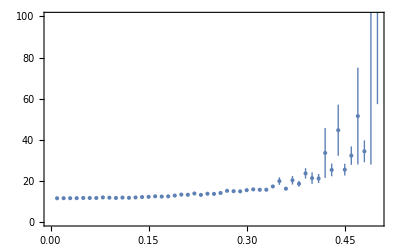

```mathematica
ListPlot[res5table, Frame -> True, PlotRange -> {{0,0.5},{0,100}}]
```

```mathematica
kf[0.5]
```

0.852245

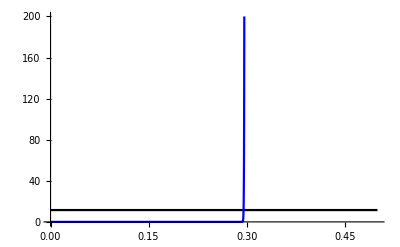

```mathematica
Plot[{11.5256,Exp[100lowBound[x,0.025,kf[0.5],100,0.01]]},{x,0,0.5}, PlotStyle -> {Black,Blue}, PlotRange -> {0,200}]
```

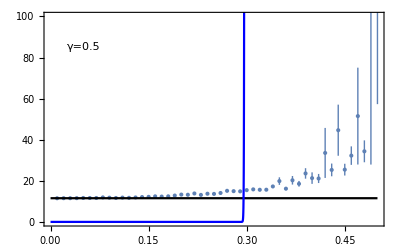

```mathematica
Show[%1407,%1400,Epilog-> {Text[Style["γ=0.5",Medium], {0.05,85}]}]
```

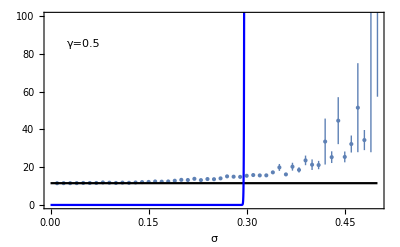

```mathematica
Show[%1410,FrameLabel->{{None,None},{HoldForm[σ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/danpirjol/statmech/jmp/BKcompounding/MCgamma0p5.eps",%1411,"EPS"]
```

/Users/danpirjol/statmech/jmp/BKcompounding/MCgamma0p5.eps

```mathematica
resLyapTable0p5={};
```

```mathematica
Do[resLyapTable0p5= Append[resLyapTable0p5, BKLyapunovSimulation[0.01 i1,0.5,100,1000]], {i1,1,50}]
```

sig= 0.01 mean = 11.5272 err = 0.00823573

sig= 0.02 mean = 11.5069 err = 0.0159035

sig= 0.03 mean = 11.5873 err = 0.0249701

sig= 0.04 mean = 11.5731 err = 0.0328803

sig= 0.05 mean = 11.553 err = 0.0402807

sig= 0.06 mean = 11.5681 err = 0.0481286

sig= 0.07 mean = 11.6874 err = 0.0569455

sig= 0.08 mean = 11.7509 err = 0.0697225

sig= 0.09 mean = 11.7523 err = 0.078037

sig= 0.1 mean = 11.8605 err = 0.0862872

sig= 0.11 mean = 11.7947 err = 0.0941231

sig= 0.12 mean = 12.048 err = 0.114786

sig= 0.13 mean = 12.1373 err = 0.124001

sig= 0.14 mean = 11.9797 err = 0.131979

sig= 0.15 mean = 12.2469 err = 0.150962

sig= 0.16 mean = 12.3905 err = 0.159218

sig= 0.17 mean = 12.5786 err = 0.173916

sig= 0.18 mean = 12.5849 err = 0.189875

sig= 0.19 mean = 12.3165 err = 0.174653

sig= 0.2 mean = 13.0846 err = 0.247404

sig= 0.21 mean = 12.7925 err = 0.225364

sig= 0.22 mean = 13.6837 err = 0.285253

sig= 0.23 mean = 13.509 err = 0.309258

sig= 0.24 mean = 13.5297 err = 0.306893

sig= 0.25 mean = 13.8422 err = 0.324146

sig= 0.26 mean = 14.252 err = 0.442875

sig= 0.27 mean = 14.6891 err = 0.399451

sig= 0.28 mean = 14.3862 err = 0.413323

sig= 0.29 mean = 14.4493 err = 0.556757

sig= 0.3 mean = 15.2763 err = 0.578327

sig= 0.31 mean = 16.232 err = 1.02772

sig= 0.32 mean = 16.0037 err = 0.700154

sig= 0.33 mean = 16.7853 err = 1.22483

sig= 0.34 mean = 17.5622 err = 1.23524

sig= 0.35 mean = 16.2997 err = 0.844988

sig= 0.36 mean = 17.9215 err = 1.01307

sig= 0.37 mean = 20.5691 err = 1.31562

sig= 0.38 mean = 20.3937 err = 2.12507

sig= 0.39 mean = 21.0017 err = 2.00396

sig= 0.4 mean = 27.2392 err = 5.50084

sig= 0.41 mean = 20.426 err = 1.32582

sig= 0.42 mean = 30.4991 err = 4.82918

sig= 0.43 mean = 175.472 err = 140.604

sig= 0.44 mean = 23.7904 err = 2.52286

sig= 0.45 mean = 27.7624 err = 6.87264

sig= 0.46 mean = 32.0583 err = 4.85203

sig= 0.47 mean = 41.4963 err = 8.26265

sig= 0.48 mean = 59.8516 err = 16.7229

sig= 0.49 mean = 72.8381 err = 36.2374

sig= 0.5 mean = 99.4982 err = 49.7659

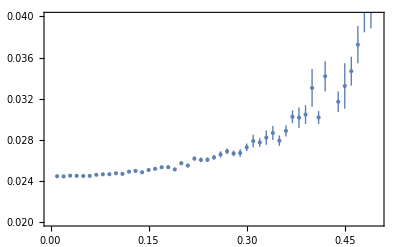

```mathematica
ListPlot[resLyapTable0p5, Frame -> True, PlotRange -> {{0.0,0.5},{0.02,0.04}}]
```

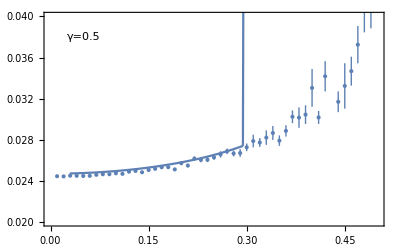

```mathematica
Show[%1417,%1330,%1331,Epilog-> {Text[Style["γ=0.5",Medium], {0.05,0.038}]}]
```

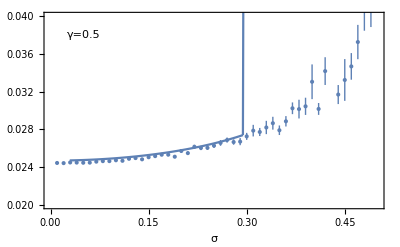

```mathematica
Show[%1418,FrameLabel->{{None,None},{HoldForm[σ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/danpirjol/statmech/jmp/BKcompounding/LyapMCgamma0p5.eps",%1419,"EPS"]
```

/Users/danpirjol/statmech/jmp/BKcompounding/LyapMCgamma0p5.eps

```mathematica
resLyapTable0p5
```

{{0.01,0.0244447},{0.02,0.0244420.000014},{0.03,0.0244730.000022},{0.04,0.0245170.000029},{0.05,0.024460.00004},{0.06,0.024540.00004},{0.07,0.024590.00005},{0.08,0.024540.00006},{0.09,0.024720.00007},{0.1,0.024700.00007},{0.11,0.024700.00008},{0.12,0.024930.00009},{0.13,0.024850.00009},{0.14,0.025150.00012},{0.15,0.025000.00011},{0.16,0.025120.00012},{0.17,0.025110.00013},{0.18,0.025270.00014},{0.19,0.025500.00016},{0.2,0.025390.00016},{0.21,0.025690.00019},{0.22,0.025720.00021},{0.23,0.025450.00021},{0.24,0.026430.00023},{0.25,0.026140.00024},{0.26,0.026440.00030},{0.27,0.026610.00027},{0.28,0.026810.00031},{0.29,0.026600.00030},{0.3,0.026760.00031},{0.31,0.02790.0005},{0.32,0.02790.0004},{0.33,0.02910.0007},{0.34,0.02910.0009},{0.35,0.02890.0006},{0.36,0.02840.0005},{0.37,0.02860.0005},{0.38,0.03020.0009},{0.39,0.03050.0010},{0.4,0.03100.0009}}

```mathematica
(* Plots for gamma=1.0 *)
```

```mathematica
Clear[res1p0table]
```

```mathematica
res1p0table={};
```

```mathematica
Do[res1p0table= Append[res1p0table, BKExpectationBnSimulation[0.01 i1,1.0,100,1000]], {i1,1,100,2}]
```

sig= 0.01 mean = 11.5294 err = 0.00532012

sig= 0.03 mean = 11.5246 err = 0.0152763

sig= 0.05 mean = 11.5355 err = 0.0280709

sig= 0.07 mean = 11.524 err = 0.0364517

sig= 0.09 mean = 11.5556 err = 0.0482503

sig= 0.11 mean = 11.7036 err = 0.058983

sig= 0.13 mean = 11.6134 err = 0.0708349

sig= 0.15 mean = 11.8705 err = 0.0861206

sig= 0.17 mean = 11.7345 err = 0.095106

sig= 0.19 mean = 11.9193 err = 0.113811

sig= 0.21 mean = 11.9353 err = 0.130111

sig= 0.23 mean = 12.1496 err = 0.140698

sig= 0.25 mean = 12.4954 err = 0.163154

sig= 0.27 mean = 12.3367 err = 0.174374

sig= 0.29 mean = 12.7664 err = 0.207371

sig= 0.31 mean = 13.2026 err = 0.24891

sig= 0.33 mean = 13.0097 err = 0.272427

sig= 0.35 mean = 13.0256 err = 0.263802

sig= 0.37 mean = 13.2434 err = 0.309031

sig= 0.39 mean = 13.9258 err = 0.350363

sig= 0.41 mean = 15.6905 err = 0.610712

sig= 0.43 mean = 13.8885 err = 0.421821

sig= 0.45 mean = 15.2235 err = 0.540731

sig= 0.47 mean = 15.419 err = 0.617825

sig= 0.49 mean = 16.102 err = 1.05027

sig= 0.51 mean = 18.2363 err = 1.71767

sig= 0.53 mean = 18.381 err = 0.878746

sig= 0.55 mean = 17.944 err = 0.941348

sig= 0.57 mean = 21.2787 err = 1.75285

sig= 0.59 mean = 21.5571 err = 2.01871

sig= 0.61 mean = 28.4403 err = 5.35894

sig= 0.63 mean = 26.8242 err = 4.6643

sig= 0.65 mean = 23.7612 err = 2.70648

sig= 0.67 mean = 23.0968 err = 2.21158

sig= 0.69 mean = 31.6646 err = 3.06535

sig= 0.71 mean = 27.4695 err = 3.31248

sig= 0.73 mean = 32.2745 err = 7.00462

sig= 0.75 mean = 28.6924 err = 2.78124

sig= 0.77 mean = 54.5251 err = 15.0462

sig= 0.79 mean = 136.802 err = 91.373

sig= 0.81 mean = 36.8978 err = 5.8343

sig= 0.83 mean = 1006.52 err = 926.354

sig= 0.85 mean = 164.028 err = 105.779

sig= 0.87 mean = 4797.27 err = 4717.2

sig= 0.89 mean = 5694.55 err = 5325.91

sig= 0.91 mean = 6.19748×10^6 err = 6.18767×10^6

sig= 0.93 mean = 187.128 err = 55.8014

sig= 0.95 mean = 3195.57 err = 3020.97

sig= 0.97 mean = 5746.86 err = 5407.36

sig= 0.99 mean = 10656. err = 10148.

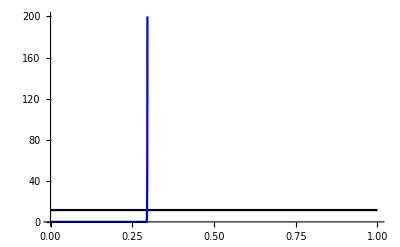

```mathematica
pth3=Plot[{11.5256,Exp[100lowBound[x,0.025,kf[0.5],100,0.01]]},{x,0,1}, PlotStyle -> {Black,Blue}, PlotRange -> {0,200}]
```

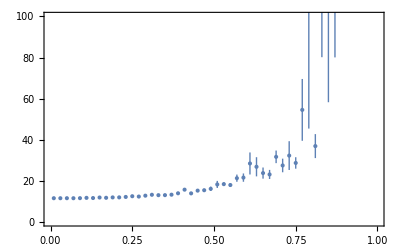

```mathematica
plotBnum3=ListPlot[res1p0table, Frame -> True, PlotRange -> {{0.0,1.0},{0.0,100}}]
```

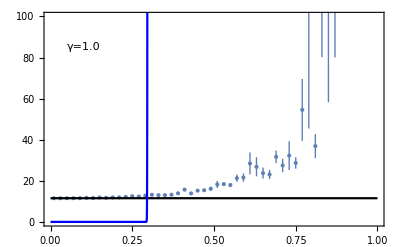

```mathematica
Show[plotBnum3,pth3,Epilog-> {Text[Style["γ=1.0",Medium], {0.1,85}]}]
```

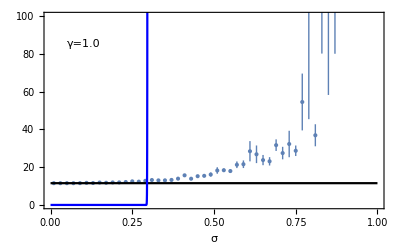

```mathematica
Show[%1578,FrameLabel->{{None,None},{HoldForm[σ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/danpirjol/statmech/jmp/BKcompounding/MCgamma1p0.eps",%1579,"EPS"]
```

/Users/danpirjol/statmech/jmp/BKcompounding/MCgamma1p0.eps

```mathematica
resLyapTable1p0={};
```

```mathematica
Do[resLyapTable1p0= Append[resLyapTable1p0, BKLyapunovSimulation[0.02 i1,1.0,100,1000]], {i1,1,50}]
```

sig= 0.02 mean = 11.5373 err = 0.0108838

sig= 0.04 mean = 11.5119 err = 0.0206537

sig= 0.06 mean = 11.5793 err = 0.0322098

sig= 0.08 mean = 11.6142 err = 0.0443295

sig= 0.1 mean = 11.6132 err = 0.0552698

sig= 0.12 mean = 11.697 err = 0.0665351

sig= 0.14 mean = 11.8538 err = 0.0802098

sig= 0.16 mean = 11.8067 err = 0.0841833

sig= 0.18 mean = 12.099 err = 0.113469

sig= 0.2 mean = 12.0459 err = 0.117725

sig= 0.22 mean = 12.0628 err = 0.132606

sig= 0.24 mean = 12.2594 err = 0.156259

sig= 0.26 mean = 12.5719 err = 0.181859

sig= 0.28 mean = 12.7739 err = 0.196694

sig= 0.3 mean = 12.5544 err = 0.218482

sig= 0.32 mean = 12.3065 err = 0.222912

sig= 0.34 mean = 13.2099 err = 0.293393

sig= 0.36 mean = 13.7049 err = 0.316853

sig= 0.38 mean = 14.675 err = 0.492782

sig= 0.4 mean = 13.459 err = 0.356592

sig= 0.42 mean = 14.6476 err = 0.451012

sig= 0.44 mean = 15.8744 err = 0.63028

sig= 0.46 mean = 15.6384 err = 0.636616

sig= 0.48 mean = 15.8109 err = 0.76689

sig= 0.5 mean = 15.8244 err = 0.655006

sig= 0.52 mean = 17.9521 err = 1.09601

sig= 0.54 mean = 19.2389 err = 1.01327

sig= 0.56 mean = 23.2588 err = 2.82522

sig= 0.58 mean = 21.4378 err = 1.66739

sig= 0.6 mean = 24.245 err = 4.65346

sig= 0.62 mean = 28.8773 err = 7.28156

sig= 0.64 mean = 20.2792 err = 1.66638

sig= 0.66 mean = 86.9384 err = 65.4254

sig= 0.68 mean = 25.0486 err = 4.17331

sig= 0.7 mean = 35.8872 err = 7.30619

sig= 0.72 mean = 56.4187 err = 19.9799

sig= 0.74 mean = 12421. err = 11520.3

sig= 0.76 mean = 74.0954 err = 25.9217

sig= 0.78 mean = 67.303 err = 33.3561

sig= 0.8 mean = 567.542 err = 501.463

sig= 0.82 mean = 191.157 err = 100.784

sig= 0.84 mean = 81.1146 err = 25.1112

sig= 0.86 mean = 1715.68 err = 1634.06

sig= 0.88 mean = 601.609 err = 307.93

sig= 0.9 mean = 153.666 err = 81.6669

sig= 0.92 mean = 2027.6 err = 1120.6

sig= 0.94 mean = 514.009 err = 259.274

sig= 0.96 mean = 306.979 err = 156.453

sig= 0.98 mean = 9070.98 err = 8202.82

sig= 1. mean = 6547.38 err = 5824.49

```mathematica
TableForm[resLyapTable1p0]
```

0.02 | 0.0244569
0.04 | 0.0244340.000018
0.06 | 0.0244920.000028
0.08 | 0.024520.00004
0.1 | 0.024520.00005
0.12 | 0.024590.00006
0.14 | 0.024730.00007
0.16 | 0.024690.00007
0.18 | 0.024930.00009
0.2 | 0.024890.00010
0.22 | 0.024900.00011
0.24 | 0.025060.00013
0.26 | 0.025310.00014
0.28 | 0.025470.00015
0.3 | 0.025300.00017
0.32 | 0.025100.00018
0.34 | 0.025810.00022
0.36 | 0.026180.00023
0.38 | 0.026860.00033
0.4 | 0.026000.00026
0.42 | 0.026840.00030
0.44 | 0.02760.0004
0.46 | 0.02750.0004
0.48 | 0.02760.0005
0.5 | 0.02760.0004
0.52 | 0.02890.0006
0.54 | 0.02960.0005
0.56 | 0.03150.0011
0.58 | 0.03070.0007
0.6 | 0.03190.0018
0.62 | 0.03360.0022
0.64 | 0.03010.0008
0.66 | 0.0450.006
0.68 | 0.03220.0015
0.7 | 0.03580.0019
0.72 | 0.04030.0030
0.74 | 0.0940.007
0.76 | 0.04310.0030
0.78 | 0.0420.004
0.8 | 0.0630.006
0.82 | 0.0530.004
0.84 | 0.04400.0027
0.86 | 0.0740.007
0.88 | 0.0640.004
0.9 | 0.0500.004
0.92 | 0.0760.004
0.94 | 0.0620.004
0.96 | 0.0570.004
0.98 | 0.0910.006
1. | 0.0880.006

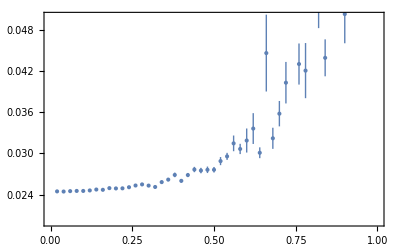

```mathematica
pnum3=ListPlot[resLyapTable1p0, Frame -> True, PlotRange -> {{0.0,1.0},{0.02,0.05}}]
```

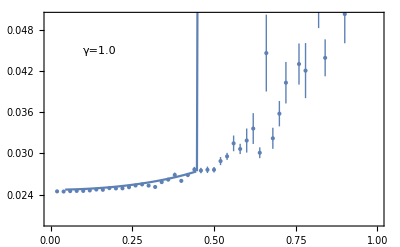

```mathematica
Show[pnum3,%1547,%1548,Epilog-> {Text[Style["γ=1.0",Medium], {0.15,0.045}]}]
```

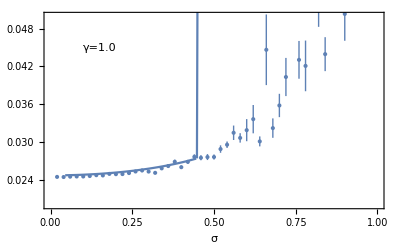

```mathematica
Show[%1551,FrameLabel->{{None,None},{HoldForm[σ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/danpirjol/statmech/jmp/BKcompounding/LyapMCgamma1p0.eps",%1552,"EPS"]
```

/Users/danpirjol/statmech/jmp/BKcompounding/LyapMCgamma1p0.eps

```mathematica
kf[a_] := (-1+a+ⅇ^-a)/a^3
```

```mathematica
sigtr[a_]:= Sqrt[-2 Log[0.025]/kf[a]/(100^2 0.01)]
```

```mathematica
sigtr[1]
```

0.447826

```mathematica
betatr[a_] := -Log[0.025]/kf[a]
```

```mathematica
betatr[1]
```

10.0274

```mathematica
?ErrorListPlot
```

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

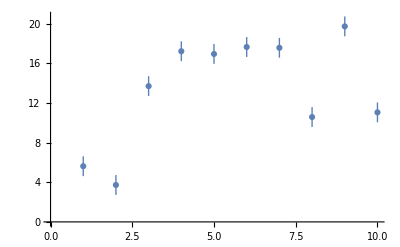

```mathematica
ListPlot[Table[Around[RandomReal[20],1],10],IntervalMarkers->"Bars"]
```

```mathematica
Table[{i,Around[RandomReal[20 i],5]},{i,1,10}]
```

{{1,17.5.},{2,32.5.},{3,32.5.},{4,14.5.},{5,19.5.},{6,69.5.},{7,97.5.},{8,16.5.},{9,56.5.},{10,76.5.}}

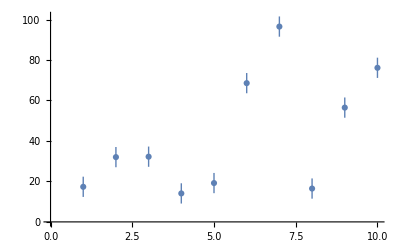

```mathematica
ListPlot[%,IntervalMarkers-> "Bars"]
```

```mathematica
Around[RandomReal[20],1]
```

15.21.0

```mathematica
?IntervalMarkers
```

```mathematica
(* a = 0.1 *)
```

```mathematica
kf[0.1]
```

4.83742

```mathematica
sigtr[0.1]
```

0.123497

```mathematica
tabLyap1sigma=Table[{Sqrt[2 betatr[0.1] 0.01 i/100], argLam[xstar1[Log[0.025],betacr[0.025,0.1] kf[0.1]0.01 i],Log[0.025],betacr[0.025,0.1] kf[0.1]0.01 i]},{i,1,100}]
```

{{0.0123497,0.0247146},{0.0174651,0.0247367},{0.0213903,0.0247588},{0.0246993,0.024781},{0.0276147,0.0248033},{0.0302504,0.0248257},{0.0326742,0.0248481},{0.0349301,0.0248707},{0.037049,0.0248933},{0.0390531,0.024916},{0.0409592,0.0249388},{0.0427805,0.0249617},{0.0445274,0.0249846},{0.0462082,0.0250076},{0.0478301,0.0250308},{0.0493987,0.025054},{0.050919,0.0250773},{0.0523952,0.0251006},{0.053831,0.0251241},{0.0552294,0.0251477},{0.0565933,0.0251713},{0.0579251,0.0251951},{0.0592269,0.0252189},{0.0605008,0.0252428},{0.0617484,0.0252668},{0.0629712,0.0252909},{0.0641708,0.0253151},{0.0653483,0.0253394},{0.066505,0.0253638},{0.0676419,0.0253883},{0.0687601,0.0254128},{0.0698603,0.0254375},{0.0709435,0.0254623},{0.0720103,0.0254871},{0.0730616,0.0255121},{0.074098,0.0255372},{0.0751201,0.0255624},{0.0761285,0.0255876},{0.0771237,0.025613},{0.0781062,0.0256385},{0.0790765,0.0256641},{0.080035,0.0256897},{0.0809822,0.0257155},{0.0819185,0.0257414},{0.0828441,0.0257675},{0.0837596,0.0257936},{0.0846651,0.0258198},{0.085561,0.0258461},{0.0864477,0.0258726},{0.0873254,0.0258991},{0.0881943,0.0259258},{0.0890548,0.0259526},{0.089907,0.0259795},{0.0907512,0.0260065},{0.0915876,0.0260337},{0.0924165,0.0260609},{0.093238,0.0260883},{0.0940523,0.0261158},{0.0948596,0.0261434},{0.0956601,0.0261712},{0.096454,0.0261991},{0.0972414,0.0262271},{0.0980225,0.0262552},{0.0987974,0.0262834},{0.0995662,0.0263118},{0.100329,0.0263403},{0.101086,0.026369},{0.101838,0.0263977},{0.102584,0.0264266},{0.103325,0.0264557},{0.10406,0.0264849},{0.10479,0.0265142},{0.105516,0.0265436},{0.106236,0.0265732},{0.106951,0.026603},{0.107662,0.0266328},{0.108368,0.0266629},{0.109069,0.026693},{0.109766,0.0267234},{0.110459,0.0267538},{0.111147,0.0267844},{0.111831,0.0268152},{0.112511,0.0268461},{0.113187,0.0268772},{0.113858,0.0269085},{0.114526,0.0269399},{0.11519,0.0269714},{0.11585,0.0270031},{0.116507,0.027035},{0.117159,0.0270671},{0.117808,0.0270993},{0.118454,0.0271317},{0.119096,0.0271642},{0.119735,0.027197},{0.12037,0.0272299},{0.121002,0.027263},{0.12163,0.0272962},{0.122256,0.0273297},{0.122878,0.0273633},{0.123497,0.0273971}}

```mathematica
xstar2[Log[0.025],kf[0.1]0.8]
```

0.980101

```mathematica
tabLyap2sigma=Table[{Sqrt[2 betatr[0.1]0.01 i/100], argLam[xstar2[Log[0.025],betacr[0.025,0.1] kf[0.1]0.01 i],Log[0.025],betacr[0.025,0.1] kf[0.1]0.01 i]},{i,100,200}];
```

```mathematica
sigtr[0.1]
```

0.123497

```mathematica
betacr[0.025,0.1]
```

0.762572

```mathematica
Sqrt[25 betatr[0.1]/100]
```

0.436627

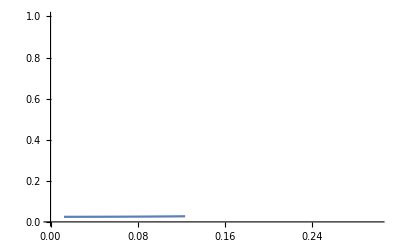

```mathematica
ListPlot[tabLyap1sigma, Joined -> True, PlotRange -> {{0,0.3},{0,1}}]
```

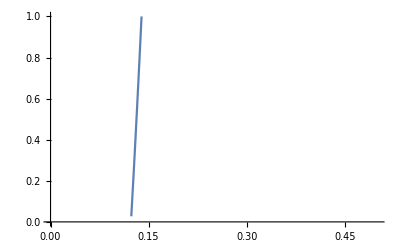

```mathematica
ListPlot[tabLyap2sigma, Joined -> True, PlotRange -> {{0,0.5},{0,1}}]
```

```mathematica
betacr[0.025,0.1]
```

0.762572

```mathematica
Sqrt[2betacr[0.025,0.1]/100]
```

0.123497

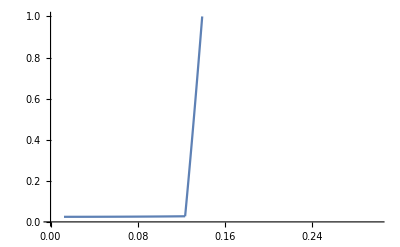

```mathematica
Show[%1318,%1321]
```

```mathematica
tabLyap0p5sigma=Table[{Sqrt[2 betatr[0.5] 0.01 i/100], argLam[xstar1[Log[0.025],betacr[0.025,0.5] kf[0.5]0.01 i],Log[0.025],betacr[0.025,0.5] kf[0.5]0.01 i]},{i,1,100}]
```

{{0.0294225,0.0247146},{0.0416097,0.0247367},{0.0509613,0.0247588},{0.058845,0.024781},{0.0657908,0.0248033},{0.0720702,0.0248257},{0.0778447,0.0248481},{0.0832195,0.0248707},{0.0882676,0.0248933},{0.0930422,0.024916},{0.0975835,0.0249388},{0.101923,0.0249617},{0.106084,0.0249846},{0.110089,0.0250076},{0.113953,0.0250308},{0.11769,0.025054},{0.121312,0.0250773},{0.124829,0.0251006},{0.12825,0.0251241},{0.131582,0.0251477},{0.134831,0.0251713},{0.138004,0.0251951},{0.141105,0.0252189},{0.14414,0.0252428},{0.147113,0.0252668},{0.150026,0.0252909},{0.152884,0.0253151},{0.155689,0.0253394},{0.158445,0.0253638},{0.161154,0.0253883},{0.163818,0.0254128},{0.166439,0.0254375},{0.16902,0.0254623},{0.171561,0.0254871},{0.174066,0.0255121},{0.176535,0.0255372},{0.17897,0.0255624},{0.181373,0.0255876},{0.183744,0.025613},{0.186084,0.0256385},{0.188396,0.0256641},{0.19068,0.0256897},{0.192936,0.0257155},{0.195167,0.0257414},{0.197372,0.0257675},{0.199553,0.0257936},{0.201711,0.0258198},{0.203845,0.0258461},{0.205958,0.0258726},{0.208049,0.0258991},{0.210119,0.0259258},{0.212169,0.0259526},{0.214199,0.0259795},{0.216211,0.0260065},{0.218203,0.0260337},{0.220178,0.0260609},{0.222135,0.0260883},{0.224075,0.0261158},{0.225999,0.0261434},{0.227906,0.0261712},{0.229797,0.0261991},{0.231673,0.0262271},{0.233534,0.0262552},{0.23538,0.0262834},{0.237212,0.0263118},{0.23903,0.0263403},{0.240834,0.026369},{0.242624,0.0263977},{0.244402,0.0264266},{0.246166,0.0264557},{0.247919,0.0264849},{0.249658,0.0265142},{0.251386,0.0265436},{0.253102,0.0265732},{0.254807,0.026603},{0.2565,0.0266328},{0.258182,0.0266629},{0.259853,0.026693},{0.261513,0.0267234},{0.263163,0.0267538},{0.264803,0.0267844},{0.266432,0.0268152},{0.268052,0.0268461},{0.269662,0.0268772},{0.271262,0.0269085},{0.272853,0.0269399},{0.274435,0.0269714},{0.276008,0.0270031},{0.277572,0.027035},{0.279127,0.0270671},{0.280673,0.0270993},{0.282211,0.0271317},{0.283741,0.0271642},{0.285262,0.027197},{0.286775,0.0272299},{0.288281,0.027263},{0.289778,0.0272962},{0.291268,0.0273297},{0.29275,0.0273633},{0.294225,0.0273971}}

```mathematica
tabLyap0p5sigma2=Table[{Sqrt[2 betatr[0.5] 0.01 i/100], argLam[xstar2[Log[0.025],betacr[0.025,0.5] kf[0.5]0.01 i],Log[0.025],betacr[0.025,0.5] kf[0.5]0.01 i]},{i,100,200}]
```

{{0.294225,0.0273971},{0.295693,0.0621759},{0.297153,0.0971287},{0.298606,0.132239},{0.300052,0.167494},{0.301491,0.202878},{0.302923,0.238383},{0.304349,0.273995},{0.305768,0.309708},{0.30718,0.345512},{0.308586,0.381399},{0.309986,0.417364},{0.311379,0.453398},{0.312766,0.489498},{0.314147,0.525657},{0.315521,0.561871},{0.31689,0.598136},{0.318253,0.634447},{0.31961,0.670802},{0.320962,0.707196},{0.322308,0.743627},{0.323648,0.780091},{0.324982,0.816587},{0.326312,0.853112},{0.327635,0.889663},{0.328954,0.926239},{0.330267,0.962838},{0.331575,0.999458},{0.332878,1.0361},{0.334176,1.07276},{0.335468,1.10943},{0.336756,1.14612},{0.338039,1.18282},{0.339317,1.21954},{0.34059,1.25627},{0.341859,1.29301},{0.343123,1.32977},{0.344382,1.36653},{0.345636,1.4033},{0.346886,1.44008},{0.348132,1.47687},{0.349373,1.51366},{0.35061,1.55046},{0.351842,1.58727},{0.35307,1.62408},{0.354294,1.6609},{0.355514,1.69773},{0.356729,1.73456},{0.35794,1.77139},{0.359148,1.80823},{0.360351,1.84507},{0.36155,1.88191},{0.362745,1.91876},{0.363937,1.95561},{0.365124,1.99246},{0.366307,2.02932},{0.367487,2.06617},{0.368663,2.10303},{0.369835,2.1399},{0.371004,2.17676},{0.372169,2.21363},{0.37333,2.25049+5.11575×10^-35 ⅈ},{0.374488,2.28736-3.2801×10^-34 ⅈ},{0.375642,2.32423-2.08×10^-32 ⅈ},{0.376792,2.36111-6.20499×10^-23 ⅈ},{0.377939,2.39798-1.43289×10^-31 ⅈ},{0.379083,2.43485+8.66668×10^-33 ⅈ},{0.380223,2.47173},{0.381359,2.5086},{0.382493,2.54548},{0.383623,2.58236},{0.384749,2.61924},{0.385873,2.65612},{0.386993,2.693},{0.38811,2.72988},{0.389223,2.76676},{0.390334,2.80364},{0.391441,2.84052},{0.392545,2.87741},{0.393647,2.91429},{0.394745,2.95117},{0.39584,2.98806},{0.396932,3.02494},{0.398021,3.06182},{0.399107,3.09871},{0.40019,3.13559},{0.40127,3.17248},{0.402347,3.20937},{0.403421,3.24625},{0.404493,3.28314},{0.405562,3.32002},{0.406627,3.35691},{0.40769,3.3938},{0.408751,3.43068},{0.409808,3.46757-8.9472×10^-22 ⅈ},{0.410863,3.50446+5.57839×10^-23 ⅈ},{0.411915,3.54135+3.56779×10^-32 ⅈ},{0.412965,3.57823+2.01419×10^-22 ⅈ},{0.414012,3.61512-3.85186×10^-33 ⅈ},{0.415056,3.65201+9.92923×10^-26 ⅈ},{0.416097,3.6889-9.2635×10^-24 ⅈ}}

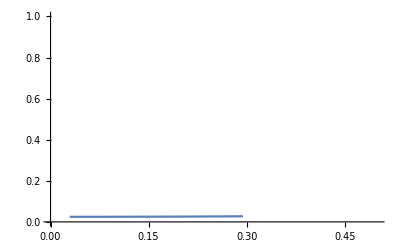

```mathematica
ListPlot[tabLyap0p5sigma, Joined -> True, PlotRange -> {{0,0.5},{0,1}}]
```

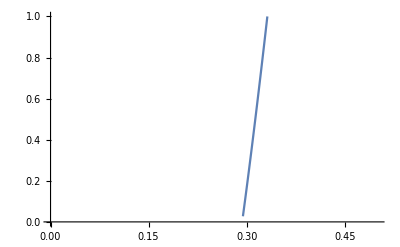

```mathematica
ListPlot[tabLyap0p5sigma2, Joined -> True, PlotRange -> {{0,0.5},{0,1}}]
```

```mathematica
tabLyap1p0sigma1=Table[{Sqrt[2 betatr[1.0] 0.01 i/100], argLam[xstar1[Log[0.025],betacr[0.025,1.0] kf[1.0]0.01 i],Log[0.025],betacr[0.025,1.0] kf[1.0]0.01 i]},{i,1,100,2}]
```

{{0.0447826,0.0247146},{0.0775658,0.0247588},{0.100137,0.0248033},{0.118484,0.0248481},{0.134348,0.0248933},{0.148527,0.0249388},{0.161466,0.0249846},{0.173442,0.0250308},{0.184643,0.0250773},{0.195203,0.0251241},{0.20522,0.0251713},{0.21477,0.0252189},{0.223913,0.0252668},{0.232697,0.0253151},{0.241162,0.0253638},{0.249339,0.0254128},{0.257257,0.0254623},{0.264938,0.0255121},{0.272402,0.0255624},{0.279667,0.025613},{0.286749,0.0256641},{0.293659,0.0257155},{0.300411,0.0257675},{0.307014,0.0258198},{0.313478,0.0258726},{0.319812,0.0259258},{0.326022,0.0259795},{0.332117,0.0260337},{0.338101,0.0260883},{0.343982,0.0261434},{0.349763,0.0261991},{0.355451,0.0262552},{0.361049,0.0263118},{0.366562,0.026369},{0.371992,0.0264266},{0.377345,0.0264849},{0.382623,0.0265436},{0.387829,0.026603},{0.392966,0.0266629},{0.398037,0.0267234},{0.403044,0.0267844},{0.407989,0.0268461},{0.412875,0.0269085},{0.417704,0.0269714},{0.422478,0.027035},{0.427199,0.0270993},{0.431868,0.0271642},{0.436487,0.0272299},{0.441058,0.0272962},{0.445581,0.0273633}}

```mathematica
tabLyap1p0sigma2=Table[{Sqrt[2 betatr[1.0] 0.01 i/100], argLam[xstar2[Log[0.025],betacr[0.025,1.0] kf[1.0]0.01 i],Log[0.025],betacr[0.025,1.0] kf[1.0]0.01 i]},{i,100,200,2}]
```

{{0.447826,0.0273971},{0.452282,0.0971287},{0.456695,0.167494},{0.461065,0.238383},{0.465395,0.309708},{0.469684,0.381399},{0.473935,0.453398},{0.478148,0.525657},{0.482324,0.598136},{0.486464,0.670802},{0.490569,0.743627},{0.49464,0.816587},{0.498678,0.889663},{0.502684,0.962838},{0.506657,1.0361},{0.5106,1.10943},{0.514513,1.18282},{0.518396,1.25627},{0.522251,1.32977},{0.526077,1.4033},{0.529875,1.47687},{0.533646,1.55046},{0.537391,1.62408},{0.54111,1.69773},{0.544804,1.77139},{0.548473,1.84507},{0.552117,1.91876},{0.555738,1.99246},{0.559335,2.06617},{0.562909,2.1399},{0.56646,2.21363},{0.56999,2.28736},{0.573497,2.36111},{0.576984,2.43485},{0.580449,2.5086},{0.583894,2.58236+6.50337×10^-27 ⅈ},{0.587319,2.65612+3.20672×10^-28 ⅈ},{0.590723,2.72988-3.58103×10^-34 ⅈ},{0.594109,2.80364},{0.597475,2.87741},{0.600822,2.95117},{0.604151,3.02494},{0.607461,3.09871},{0.610753,3.17248},{0.614028,3.24625},{0.617286,3.32002},{0.620526,3.3938},{0.62375,3.46757},{0.626957,3.54135},{0.630147,3.61512},{0.633322,3.6889}}

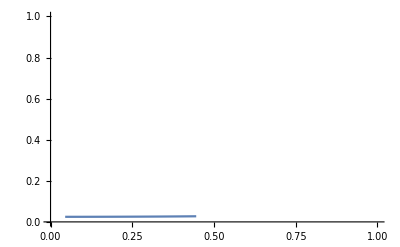

```mathematica
ListPlot[tabLyap1p0sigma1, Joined -> True, PlotRange -> {{0,1.0},{0,1}}]
```

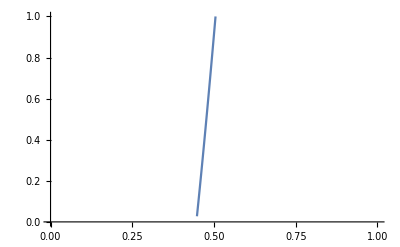

```mathematica
ListPlot[tabLyap1p0sigma2, Joined -> True, PlotRange -> {{0,1.0},{0,1}}]
```

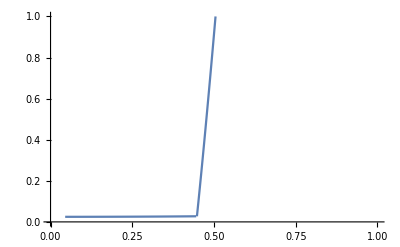

```mathematica
Show[%1547,%1548]
```